# Data and function visualization

## Basic setup

First, import the latest version from GitHub.

```mathematica
Import["https://raw.githubusercontent.com/jonasmusall/sciplot/main/SciPlot.m"]
```

SciPlot can be used to create plots of functions and of lists of points. Note that the function and the specification for its argument are enclosed in a list together.

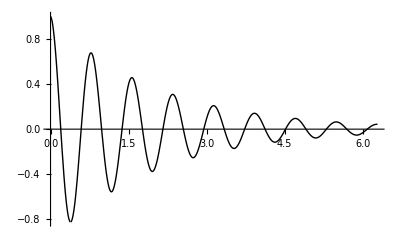

```mathematica
f[x_]:=Cos[8x]Exp[-x/2]
SciPlot[{f[x],{x,0,2Pi}}]
```

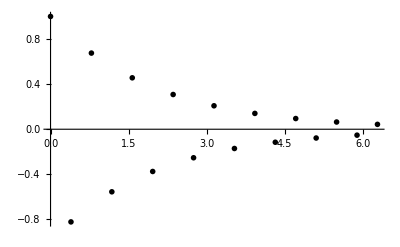

```mathematica
data1=Table[{x,f[x]},{x,0,2Pi,Pi/8}];
SciPlot[data1]
```

Supply a sequence of datasets and functions to plot them together.

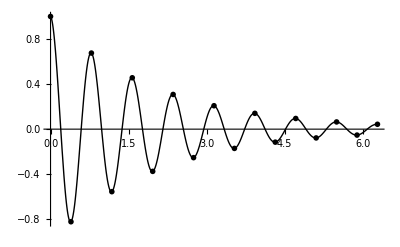

```mathematica
SciPlot[{f[x],{x,0,2Pi}},data1]
```

## Options

### AxesLabel

Labels which are automatically placed according to the position of the axes. Use a pair of labels to put one on each axis.

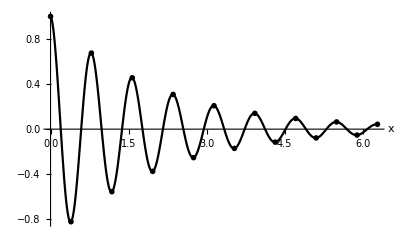
-Graphics-ⅇ^(-x/2) cos(8 x)

```mathematica
SciPlot[{f[x],{x,0,2Pi}},data1,AxesLabel->{x,f[x]//TraditionalForm}]
```

### AxesOrigin

Point where the axes cross. Default value is Automatic, which may place the origin at a different point than {0,0} depending on the plot contents.

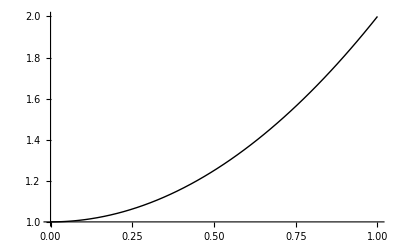

```mathematica
SciPlot[{x^2+1,{x,0,1}}]
```

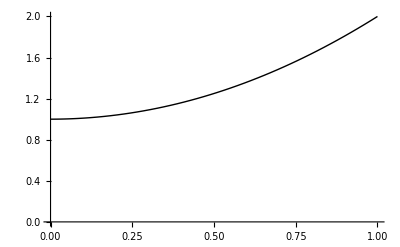

```mathematica
SciPlot[{x^2+1,{x,0,1}},AxesOrigin->{0,0}]
```

### PlotRange

Range to display in the plot. Valid values are ranges for both direction {{x_min,x_max},{y_min,y_max}} or Automatic.

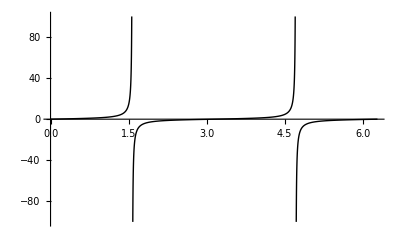

```mathematica
SciPlot[{Tan[x],{x,0,2Pi}},PlotRange->{{0,2Pi},{-100,100}}]
```

### PlotStyle

Style for the plots to be drawn in. Specify a single style to be applied to all plots or a list of styles.

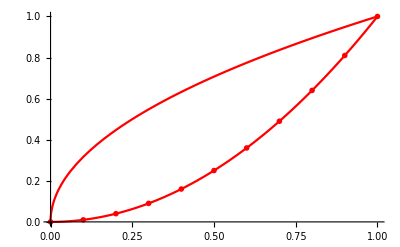

```mathematica
SciPlot[{{x^(1/2),x^2},{x,0,1}},Table[{x,x^2},{x,0,1,0.1}],PlotStyle->Red]
```

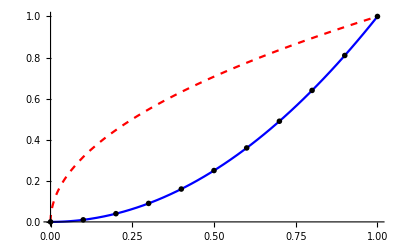

```mathematica
SciPlot[{{x^(1/2),x^2},{x,0,1}},Table[{x,x^2},{x,0,1,0.1}],PlotStyle->{{Red,Dashed},Blue,Black}]
```